# Correlation Intuition

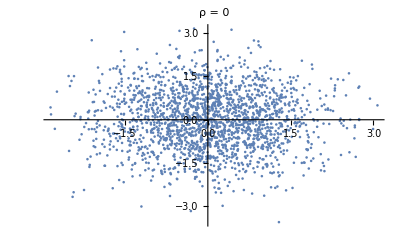
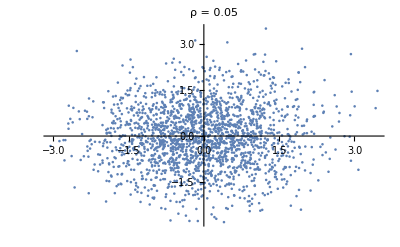
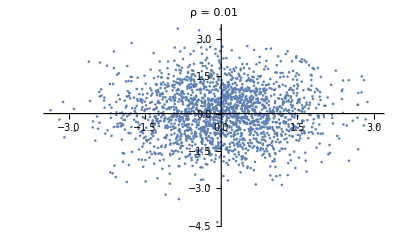
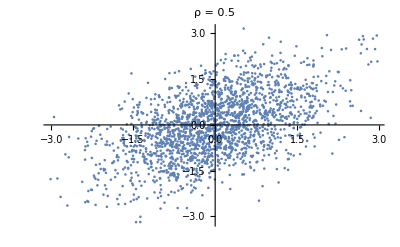
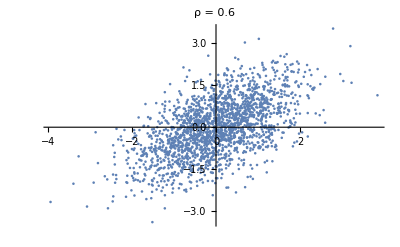
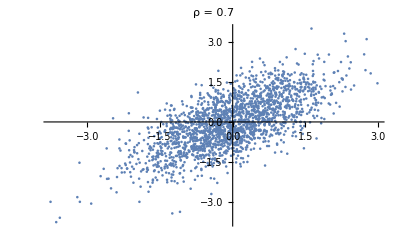
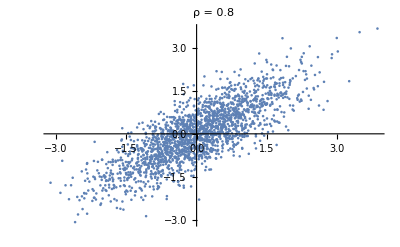
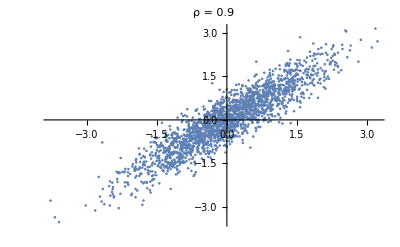

```mathematica
Table[ListPlot[RandomVariate[BinormalDistribution[p],2000],PlotLabel->Row[{"ρ = ",p}]],{p,{0,0.05,0.01,0.5,0.6,0.7,0.8,0.9,0.9999}}]
```

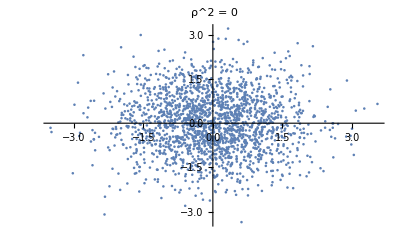
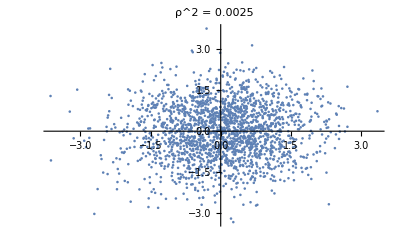
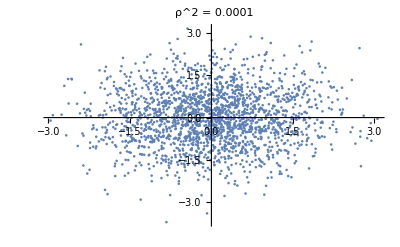
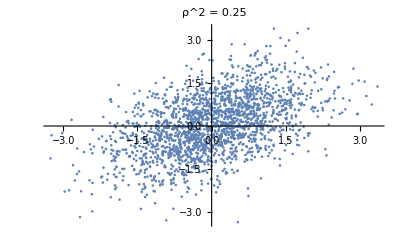
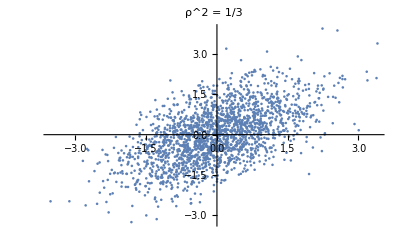
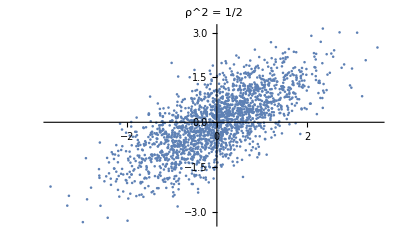
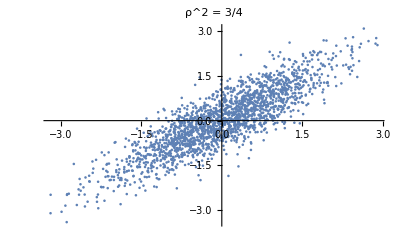
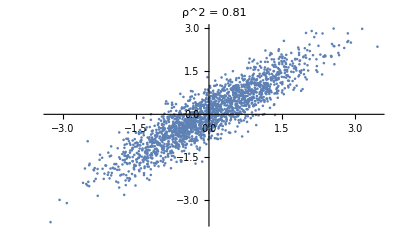

```mathematica
Table[ListPlot[RandomVariate[BinormalDistribution[p],2000],PlotLabel->Row[{"ρ^2 = ",p^2}]],{p,{0,0.05,0.01,0.5,Sqrt[1/3],Sqrt[1/2],Sqrt[3/4],0.9,0.9999}}]
```

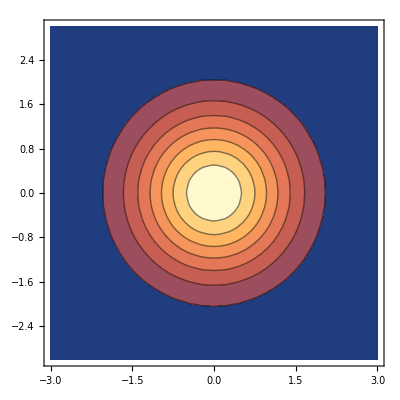
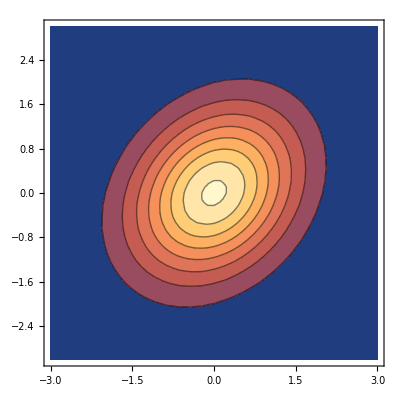
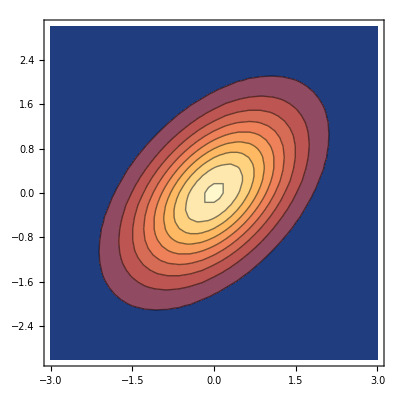
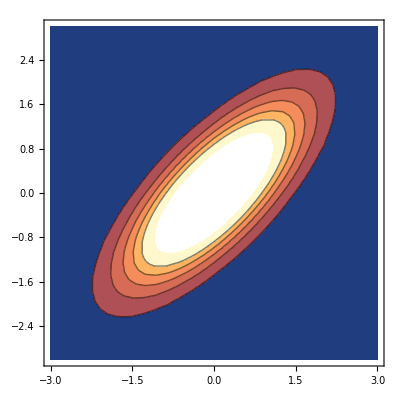
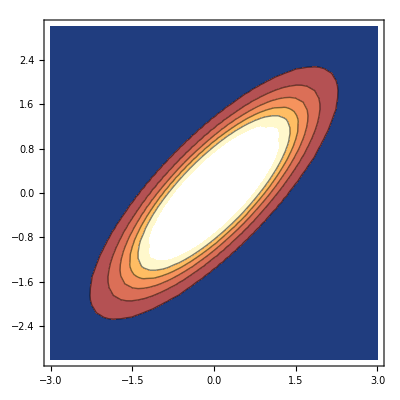
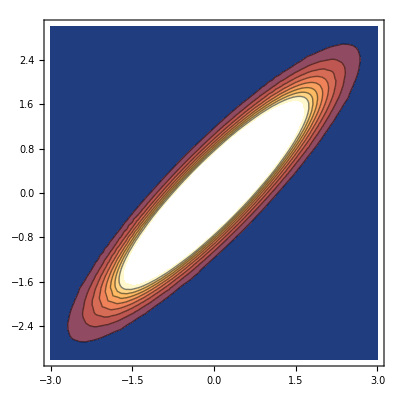
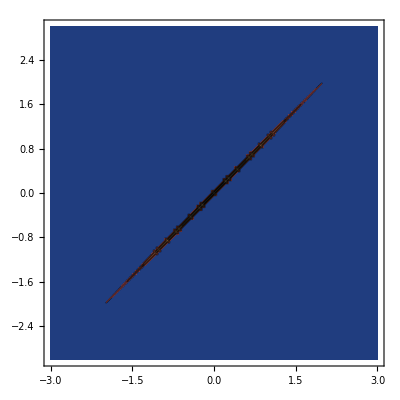
{{0,-Graphics-},{1/4,-Graphics-},{1/2,-Graphics-},{3/4,-Graphics-},{4/5,-Graphics-},{9/10,-Graphics-},{999999999/1000000000,-Graphics-}}

```mathematica
Table[{ρ,ContourPlot[PDF[BinormalDistribution[ρ],{x,y}],{x,-3,3},{y,-3,3}]},{ρ,{0,1/4,1/2,3/4,8/10,9/10,999999999/1000000000}}]
```

## Mutual Information

Does not look like really twice to me.

```mathematica
ρ[m_]:=√(1-Exp[-2m])
```

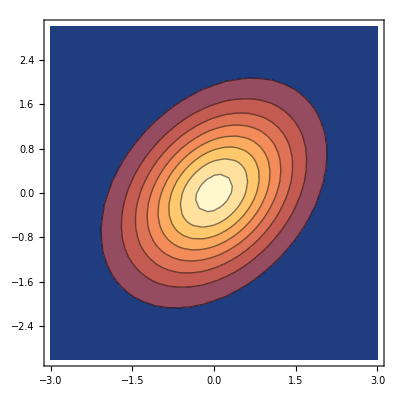
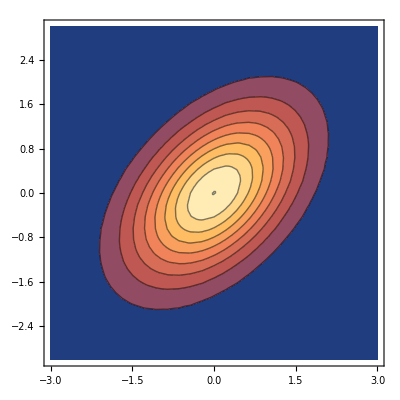
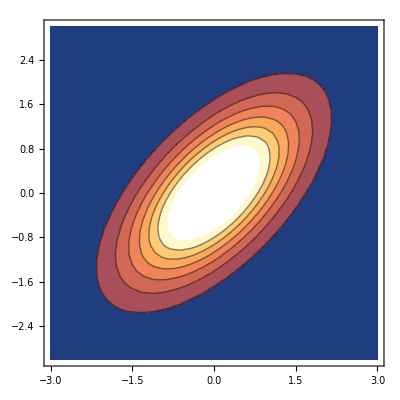
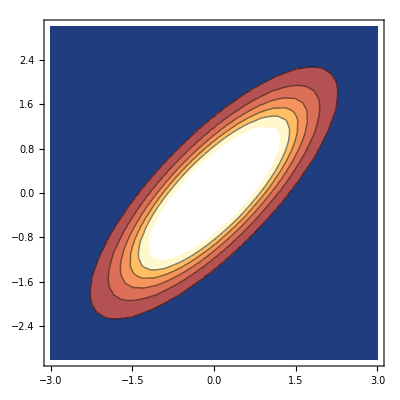
{{ρ,-Graphics-},{ρ,-Graphics-},{ρ,-Graphics-},{ρ,-Graphics-},{ρ,-Graphics-}}

```mathematica
Table[{ρ,ContourPlot[PDF[BinormalDistribution[ρ[g]],{x,y}],{x,-3,3},{y,-3,3}]},{g,{0,1/16,1/8,1/4,1/2}}]
```

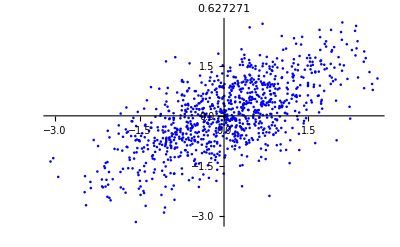

```mathematica
ListPlot[RandomVariate[BinormalDistribution[ρ[1/4]],1000], PlotStyle->Blue, AxesLabel -> ρ[1/4]//N]
```

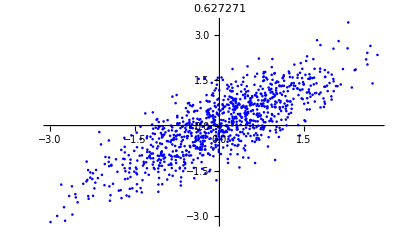

```mathematica
ListPlot[RandomVariate[BinormalDistribution[ρ[1/2]],1000], PlotStyle->Blue, AxesLabel -> ρ[1/4]//N]
```

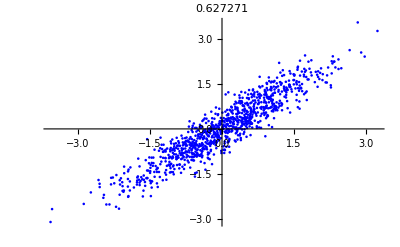

```mathematica
ListPlot[RandomVariate[BinormalDistribution[ρ[1]],1000], PlotStyle->Blue, AxesLabel -> ρ[1/4]//N]
```

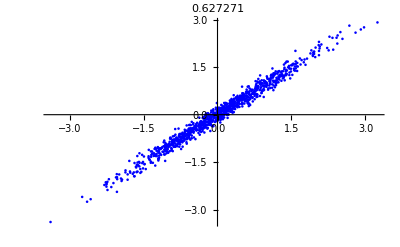

```mathematica
ListPlot[RandomVariate[BinormalDistribution[ρ[1/0.5]],1000], PlotStyle->Blue, AxesLabel -> ρ[1/4]//N]
```

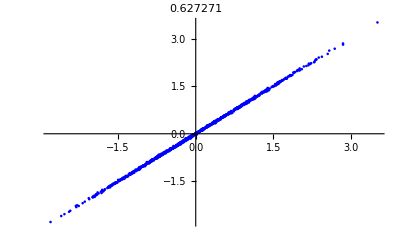

```mathematica
ListPlot[RandomVariate[BinormalDistribution[ρ[1/0.25]],1000], PlotStyle->Blue, AxesLabel -> ρ[1/4]//N]
```